```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Quiet[Needs["PhysicalConstants`"]];
ee=ElectronCharge/Coulomb;
hp=PlanckConstant/(2 π Joule Second);
eEf=11200;
cm=0.01;
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={010119,10124,10166,10189,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,11159,11166,11239,11277,11305,11357,11363,11409,11412}];(*{010119,10124,10135,10166,10189,10191,10207,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,10541},{11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448},{11159,11166,11239,11277,11305,11357,11363,11409,11412}*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;ChNum=1;
chnum={1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19};
steps={28,2,2,2,2,20,160,2,2,64,1};(**)
Print["Number of Steps: ",Dimensions[steps][[1]]];
(*6->HV, SF1->25, SF2->26, cRF->-1, UP->27, DOWN->28, Monitor->30, Filling->31, Total->32*)
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10119,10124,10166,10189,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,11159,11166,11239,11277,11305,11357,11363,11409,11412}

#Runs in the list: 25

Number of Steps: 11

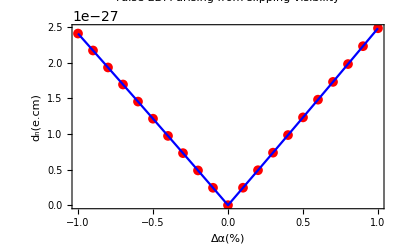

```mathematica
pt1[xx_,aa_]=N[5000(1+(aa Cos[3-7xx]))];
pt2[xx_,aa_]=N[5000(1-(aa Cos[3-7xx]))];
al[xx_,aa_]=(pt1[xx,aa]-pt2[xx,aa])/(pt1[xx,aa]+pt2[xx,aa]);
Clear[nlm,p,af];
nlm[per_]:=FindFit[{{30.23,al[30.23,1]},{30.32,al[30.32,1-per]},{30.68,al[30.68,1-2per]},{30.77,al[30.77,1-3per]}}, af Cos[3-7xx-p],{af,p},xx];
pttab=Table[{100k,Abs[(hp cm (p/.nlm[k]))/(4(ee eEf) Sqrt[10000])]},{k,-.01,.01,.001}];(*Scaled down to 10000*)
Show[{
ListPlot[pttab,PlotStyle->Red,Frame->True,PlotMarkers->{Automatic,10},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},PlotLabel->"False EDM arising from slipping visibility",ImageSize->{1000},PlotRange->Full,FrameLabel->{"Δα(%)","d_n(e.cm)"}],
ListLinePlot[pttab,PlotStyle->Blue,ImageSize->1200,Frame->True,InterpolationOrder->1,TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},PlotLabel->"False EDM arising from slipping visibility",ImageSize->{1000},PlotRange->Full,FrameLabel->{"Δα(%)","d_n (e.cm)"}]
}]
```

```mathematica
FullSimplify[al[x,a]]
```

1. a Cos[3.-7. x]

```mathematica
Abs[(hp cm (p/.nlm[k]))/(4(ee eEf)Sqrt[10000])];
```